```mathematica
(*R is the radius, interval is [-R,R]*)
R=30;
(*intervals*)
M=1000;
(*sites is intervals + 1*)
sites=M+1;
ϵ=1;
a=1;
(*electron density function*)
ρ[r_]=If[r>=0,1/(π a^3)ⅇ^(-2 r/a),1/(π a^3)ⅇ^(2 r/a)];
(*integrals that come from integrating the electron density and everything*)
int[R_,v_,a1_,a2_]:=NIntegrate[1/ϵ r^2 ρ[r]*v,{r,a1,a2}];
(*interval length*)
Δx=(2*R)/M;
(*defines elements*)
linFunc[a_,r_]:=If[r<a,1/Δx(r-a)+1,-1/Δx(r-a)+1];
RealFunction[r_]=1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a));
```

```mathematica
(*Making a table of elements in the vector on the RHS*)
RHS=Table[int[R,linFunc[i,r],i,i+Δx],{i,-R+Δx,R-Δx,Δx}];
```

```mathematica
(*check dimensions*)
b=RHS;
Dimensions[b]
(*Remove the first 2 rows and last 2 rows because of boundary conditions?*)
(*check dimen
sions*)
```

{999}

```mathematica
(*define array of zeroes*)
LHS=ConstantArray[0,{sites,sites}];
(*define m_k (the factor in each element of the matrix*)
mk[j_]=((-R+Δx*j)^3-(-R+Δx*j-Δx)^3)/(3 Δx^2);
(*create a loop to fill in elements*)
For[i=0,i<sites,i++,
If[i+1<=sites&&i>0,LHS[[i+1,i]]=-mk[i]];
If[i+1<=sites&&i>=0,LHS[[i+1,i+1]]=mk[i+1]+mk[i]];
If[i+2<=sites,LHS[[i+1, i+2]]=-mk[i+1]];
]
```

```mathematica
LHS//MatrixForm;
```

```mathematica
(*check dimensions*)
Dimensions[LHS]
```

{1001,1001}

```mathematica
(*check dimensions*)
Dimensions[b]
```

{999}

```mathematica
LHS=Delete[LHS,{{1},{sites}}];
(*delete the first and last columns in the matrix*)
LHS=Drop[LHS,None,{1,1}];
LHS=Drop[LHS,None,{sites-1,sites-1}];
```

```mathematica
(*solve the system*)
system=LinearSolve[LHS,b];
```

```mathematica
listOfR=Table[-R+Δx*j,{j,1,M-1} ];
```

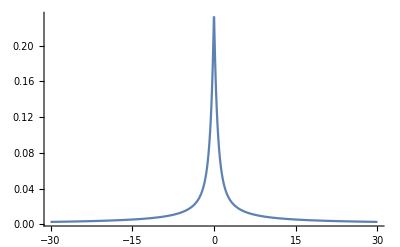

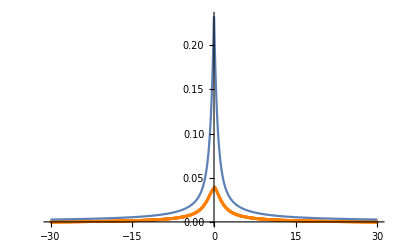

```mathematica
temp1=ListPlot[Transpose[{listOfR,system}],PlotStyle->{Orange}];
temp2=Plot[If[r>0,1/(4π ϵ a^2)(a^2/r-(a^2/r-a)ⅇ^(-2 r/a)),1/(4π ϵ a^2)(-a^2/r-(-a^2/r-a)ⅇ^(2 r/a))],{r,-R,R},PlotRange->All]
Show[temp1,temp2,PlotRange->All]
```

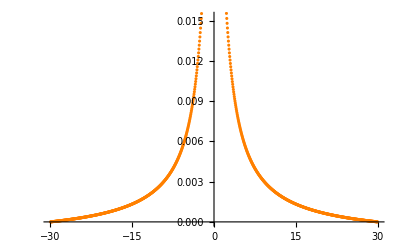

```mathematica
temp1
```